```mathematica
(*Rutina generaliza de Kaprekar*)
kaprekar[n_,k_]:=FromDigits[PadRight[Reverse[Sort[IntegerDigits[k]]],If[n-Length[IntegerDigits[k]]==0,Length[IntegerDigits[k]],n]]]-FromDigits[PadLeft[Sort[IntegerDigits[k]],If[n-Length[IntegerDigits[k]]==0,Length[IntegerDigits[k]],n]]];
```

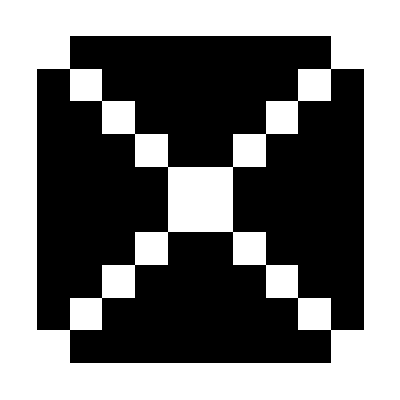

```mathematica
(*Alfombra para dos cifras*)
count2[n_,k_]:=If[Or[kaprekar[n,k]==0,Count[{9,18,27,36,45},FromDigits[Sort[IntegerDigits[k]]]]==1],0,i=0;Subscript[c, 0]=k;While[Count[{9,18,27,36,45},FromDigits[Sort[IntegerDigits[Subscript[c, i]]]]]≠1,Subscript[c, i+1]=kaprekar[n,Subscript[c, i]];i=i+1];i]data2=Table[count2[2,10*x+y],{x,0,9},{y,0,9}];ArrayPlot[data2]
```

```mathematica
(*Alfombra para tres cifras(Version 3D)*)
count3[n_,k_]:=If[Or[kaprekar[n,k]==0,k==495],0,i=0;Subscript[c, 0]=k;While[Subscript[c, i]≠495,Subscript[c, i+1]=kaprekar[n,Subscript[c, i]];i=i+1];i];data3d=Table[count3[3,100*x+10*y+z],{x,0,9},{y,0,9},{z,0,9}];ArrayPlot3D[data3d,ColorRules->{0->RGBColor["#FFFFFF"],1->RGBColor["#FEDB01"],2->RGBColor["#4AFD04"],3->RGBColor["#02FE94"],4->RGBColor["#0191FD"],5->RGBColor["#4501FE"],6->RGBColor["#FF00DC"],7->RGBColor["#FE0000"]}]
```

-Graphics3D-

```mathematica
(*Alfombra para tres cifras (Version 2D)*)
lpac={};For[w=0,w<=9,w++,AppendTo[lpac,Table[count3[3,10*x+y],{x,w*10,w*10+9},{y,0,9}]]];Animate[ArrayPlot[lpac[[a]],ColorRules->{0->RGBColor["#FFFFFF"],1->RGBColor["#FEDB01"],2->RGBColor["#4AFD04"],3->RGBColor["#02FE94"],4->RGBColor["#0191FD"],5->RGBColor["#4501FE"],6->RGBColor["#FF00DC"]}],{a,1,Length[lpac],1}]
```